## Load Libraries and Create The Model

## Load Libraries

```mathematica
(* core RBD & NCM library *)
SetDirectory[FileNameJoin[{NotebookDirectory[], "../../"}]];
<< "SIMple`";

(* dynamics + NCM helper functions, see CompassGaitWithActuator.nb for model information *)
SetDirectory[FileNameJoin[{NotebookDirectory[], "../"}]];
<< "CompassGaitWithActuator`";
```

## Compile Biped

Refer to CompassGait/Main.nb for detailed description of this code.

```mathematica
n = 1;
CompassGaitWithActuator[n]; // AbsoluteTiming
```

RigidBodyDynamics`Private`PreprocessConstraints::name: No valid constraints found under left-ηv.

RigidBodyDynamics`Private`PreprocessConstraints::name: No valid constraints found under right-ηv.

{80.9097,Null}

## Load Gaits (optional)

load pre-computed gaits; loading gaits will load the following variables (these are the same variable names used in the section “Generate Gaits”):

variable name		|  description
---------------------------------------------------------------------------------------------------------
man1			|  branches of passive gaits (u = 0) emanating from 1st bifurcation point
man2			|  branches of passive gaits (u = 0) emanating from 2nd bifurcation point
root				|  branches of gaits  with final gait walking on flat ground
aman			|  branches of powered gaits (u != 0)

NOTE: You can skip the next code block, Genera Gaits, if you load these gaits.

```mathematica
BLGetFrom["Here", "cgwa.mx"];
```

## Generate Gaits

## Generate Passive Gaits

### Find singular equilibrium gaits on u = 0 slice

NOTE: For new models, setting Tsearch = {0, 1} is recommended as an initial value.  After the SEGs are found, you can narrow the window to speed up future searches.

{0.624159,0.68465}

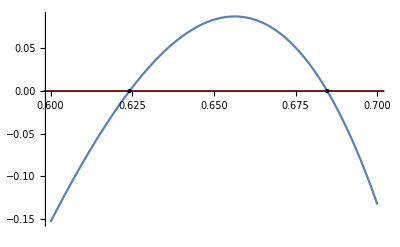

```mathematica
Tsearch = {0.6, 0.7}; (* narrow search to all SEGs in (0, 1] *)
{TR, PL} = BLFindBifurcation[CompassGaitWithActuatorP, Tsearch]⟦{1,3}⟧;

(* all switching times *)
TR
(* plot *)
PL
```

### Continuation Options

```mathematica
(* fixed step size *)
h = {1/20.};
(* option value for setting value of "0" for NullSpace function *)
tol = 10^-8.;
(* # of points on curve to generate *)
m = 250;
```

### Trace passive gaits (u = 0) intersecting first switching time

```mathematica
(* SEG switching time *)
T = TR⟦1⟧;

(* call driver function for generating continuum of bipedal walking gaits *)
(* Evaluation -> Abort Evaluation (ALT + .) to return current set of gaits *)
man1 = BLGenerateGaits[CompassGaitWithActuatorP, T, h, m, Man-> {Method -> cmc, Monitor -> tmon, "nstol" -> tol}];

man1 = Select[man1, # =!= $Failed&];
```

depth: 188 nodes: 375 nodes per second: 3.352 elapsed time: 111.900

### Animate a gait from man1

```mathematica
BLWalk[man1, {-50}, 3] (* can use keys or indices to view a gait *)
```

### Trace passive gaits (u = 0) intersecting second switching time

```mathematica
(* SEG switching time *)
T = TR⟦2⟧;

(* driver function for generating continuum of bipedal walking gaits *)
(* Evaluation -> Abort Evaluation (ALT + .) to return current set of gaits *)
man2 = BLGenerateGaits[CompassGaitWithActuatorP, T, h, m, Man-> {Method -> cmc, Monitor -> tmon, "nstol" -> tol}];

man2 = Select[man2, # =!= $Failed&];
```

### Animate a gait from man2

```mathematica
BLWalk[man2, {25}, 3]
```

## Generate Actuated Gaits

### Functions for computing actuated gaits

```mathematica
CompPN[M_, m_:25] := Join[CompNeg[M, m], CompPos[M, m]];
CompPos[M_, m_:25] := CompA[KeySelect[M, Positive@First[#]&], m];
CompNeg[M_, m_:25] := CompA[KeySelect[M, Negative@First[#]&], m];

CompA[M_, m_:25] := Module[{c, T, man},
Table[
c = M⟦k, 1⟧;
T = c⟦-1⟧;

(* redefine map with fixed switching time to be fixed at switch time T *)
CompassGaitWithActuatorA[T];

man = BLGenerateGaits[CompassGaitWithActuatorA, c, h, m, Man-> {Method -> cmc, Monitor -> tmon, "nstol" -> tol,"cm" -> {"newton" -> {Print -> 25}}}];

Select[man, # =!= $Failed&],

{k, Length@M}
]
];
```

### Compute actuated gaits using man1 as seed values

```mathematica
a1 = 2Range[2, 250, 4]+1;
a1 = Join[a1-1, a1];
aman1 = CompPN[man1⟦a1⟧, 50];
```

### Animate a gait from aman1

```mathematica
BLWalk[aman1⟦5⟧, {25}, 3]
```

### Compute actuated gaits using man2 as seed values

```mathematica
a2 = 2Range[2, 114, 4]+1;
a2 = Join[a2-1, a2];
aman2 = CompPN[man2⟦a2⟧, 50];
```

### Animate a gait from aman2

```mathematica
BLWalk[aman2⟦5⟧, {25}, 3]
```

## Global Homotopy Map

### Helper functions

```mathematica
step[A_Association] := Module[{X0, XT},
X0 = A["c"]⟦1⟧;
XT = A["c"]⟦-1⟧;
XT⟦All, 2;;2⟧ - X0⟦All, 2;;2⟧
]

step[c_, m_:Automatic] := Module[{mp, C0, CT},
mp = If[m === Automatic, BLbiped["m[0]"], m];
C0 = devec[BLmxcp[mp, c]⟦3⟧, nc];
CT = devec[BLmxc0[mp, c]⟦3⟧, nc];
CT⟦All, 2;;2⟧ - C0⟦All, 2;;2⟧
]

slope[A_Association] := Module[{m, X, C, S},
m = A["m"]⟦1⟧;
X = A["x-"]⟦1⟧;
C = A["c"]⟦1⟧;
S = devec[BLbiped["σ", m][X, C], mm];
S⟦All, mm;;mm⟧
];

slope[c_, m_:Automatic] := Module[{mp, X, C, S},
mp = If[m === Automatic, BLbiped["m[0]"], m];

C = devec[BLmxcp[mp, c]⟦3⟧, nc];
S = devec[BLbiped["σ", mp][C⟦All, 1;;nx⟧, C], mm];
S⟦All, mm;;mm⟧
];
```

### Map of desired gait properties

```mathematica
(* homotopy map *)
Options[H] = {Map -> {}};
H[mp_String, cp_, opts:OptionsPattern[]] := Module[{M, X, C, S},
M = OptionValue[Map];
If[M === {}, M = BLP[mp, cp, opts];];
S = slope[M];
S = {Sin[S⟦1⟧ - σdes], Cos[S⟦1, 1⟧]S⟦2⟧};
X = step[M];
X = {X⟦1⟧-xdes, X⟦2⟧};
MapThread[Join, {S, X}]
];
```

### GHM using man1

```mathematica
k = 46;
c = man1⟦k, 1⟧;

(* desired gait properties *)
σdes = 0; (* walk on flat ground *)
xdes = 0.65step[c]⟦1,1⟧; (* 65% of c's step size *)

rootopts = {"cm" -> {Print -> 1, "max" -> 10, Root -> True}};

root1 = BLGlobalHomotopy[{BLP, H}, c, {0}, 1000, Man -> rootopts];
root1 = Select[root1, # =!= $Failed&];
```

```mathematica
BLWalk[root1, -1, 2]
```

### GHM using man2

```mathematica
k = 46;
c = man2⟦k, 1⟧;

(* desired gait properties *)
σdes = 0; (* walk on flat ground *)
xdes = 0.5step[c]⟦1,1⟧; (* 50% of c's step size *)

rootopts = {"cm" -> {"β" -> 0.5, "min" -> 0, Print -> 1, "max" -> 10, Root -> True}};

root2 = BLGlobalHomotopy[{BLP, H}, c, {0}, 1000, Man -> rootopts];
root2 = Select[root2, # =!= $Failed&];
```

```mathematica
BLWalk[root2, -1, 2]
```

## Save Gaits

save computed gaits

variable name		|  description
---------------------------------------------------------------------------------------------------------
man1			|  branches of passive gaits (u = 0) emanating from 1st bifurcation point
man2			|  branches of passive gaits (u = 0) emanating from 2nd bifurcation point
root				|  branches of gaits  with final gait walking on flat ground
aman			|  branches of powered gaits (u != 0)

NOTE: The call to Save[...] will overwrite previous file.  Uncomment to use.  Recomment to avoid overwriting data.

```mathematica
(* uncomment to actually save; should recomment when done. *)
BLSaveTo["Here", "cgwa.mx", {man1, man2, root1, root2, aman1, aman2}]
```